# Cell Complex Thinning

CSE 554 Module 2, Washington University in St. Louis (Fall 2015)

## Introduction

Thinning is one of the most commonly used methods for extracting skeletons of a solid object. Here you will experiment with thinning on 2D and 3D binary pictures using a geometric representation called Cell Complexes. This representation allows you to write simple thinning code that works on objects in any dimensions.

## Helpers

### Importing images

Sets the default folder to be the folder where this notebook is saved.

```mathematica
SetDirectory[ToFileName[Extract["FileName"/.NotebookInformation[EvaluationNotebook[]],{1},FrontEnd`FileName]]];
```

Constructs a 2D array from input RGB color images by extracting the Red component of each pixel.

```mathematica
PNGtoGray[filename_]:=Reverse[Map[Map[First,#]&,Import[filename,"Data"]]];
```

```mathematica
GIFtoGray[filename_]:=255-Reverse[Map[Map[First,#]&,Import[filename,"Data"]]];
```

### Showing images

Shows a binary image (with only values 0, 1)

```mathematica
showBinaryImage[bimg_]:=Graphics[Raster[bimg],Frame->False];
```

Shows a grayscale image

```mathematica
showGrayImage[img_]:=Graphics[Raster[img/Max[img]],Frame->False];
```

### Showing cell complexes

#### Some helper functions

Given a list of edges around the face, each as a pair of vertex indices, returns a single list of vertex indices that trace the face boundary:

```mathematica
traceFace[edgelist_]:=Module[{face=edgelist⟦1⟧,p,nlist=Drop[edgelist,1]},
While[Length[nlist]>1,
p=Position[nlist,Last[face]];
AppendTo[face,nlist⟦p⟦1,1⟧,3-p⟦1,2⟧⟧];
nlist=Drop[nlist,{p⟦1,1⟧}]];
face];
```

This function gets the scale of the cell complex (as the length of the largest side of the bounding box), for properly scaling the size of visual elements like point sizes and edge thickness:

```mathematica
getScale[cc_]:=Max[Map[(Max[#]-Min[#]+1)&,Transpose[cc⟦1⟧]]];
```

Obtains the exterior faces of a 3D complex for faster visulization:

```mathematica
getExteriorFaces[cc_]:=Module[{val},
val=Map[0&,cc⟦3⟧];
Scan[Scan[val⟦#⟧++&,#]&,cc⟦4⟧];
Pick[cc⟦3⟧,Map[(#<2)&,val]]];
```

#### 2D

Options for 2D visualization:

```mathematica
ptSize2D=0.02;ptColor2D=GrayLevel[0];ptColorOri2D=GrayLevel[0.85];
edgeSize2D=0.01;edgeColor2D=GrayLevel[.2];edgeColorOri2D=GrayLevel[0.9];faceColor2D=GrayLevel[0.5];faceColorOri2D=GrayLevel[0.95];
```

Shows a 2D cell complex:

```mathematica
showCC2D[cc_]:=Module[{scl=getScale[cc]/10.0,len=Length[cc]},
Graphics[{
If[len≥3,{faceColor2D,EdgeForm[{}],Map[Polygon[cc⟦1,traceFace[cc⟦2,#⟧]⟧]&,cc⟦3⟧]},{}],
If[len≥2,{edgeColor2D,Thickness[edgeSize2D/scl],Map[Line[cc⟦1,#⟧]&,cc⟦2⟧]},{}],
{ptColor2D,PointSize[ptSize2D/scl],Map[Point,cc⟦1⟧]}}]];
```

Shows one 2D cell complex (cc1) overlaying another (cc2), with cc2 drawn in lighter colors in the backbround:

```mathematica
showCC2D[cc1_,cc2_]:=Module[{scl=getScale[cc2]/10.0,len1=Length[cc1],len2=Length[cc2]},
Graphics[{
If[len2≥3,{faceColorOri2D,EdgeForm[{}],Map[Polygon[cc2⟦1,traceFace[cc2⟦2,#⟧]⟧]&,cc2⟦3⟧]},{}],
If[len2≥2,{edgeColorOri2D,Thickness[edgeSize2D/scl],Map[Line[cc2⟦1,#⟧]&,cc2⟦2⟧]},{}],
{ptColorOri2D,PointSize[ptSize2D/scl],Map[Point,cc2⟦1⟧]},
If[len1≥3,{faceColor2D,EdgeForm[{}],Map[Polygon[cc1⟦1,traceFace[cc1⟦2,#⟧]⟧]&,cc1⟦3⟧]},{}],
If[len1≥2,{edgeColor2D,Thickness[edgeSize2D/scl],Map[Line[cc1⟦1,#⟧]&,cc1⟦2⟧]},{}],
{ptColor2D,PointSize[ptSize2D/scl],Map[Point,cc1⟦1⟧]}}]];
```

Shows one 2D cell complex overlaying an image:

```mathematica
showCC2DImg[cc_,img_]:=Module[{scl=getScale[cc]/10.0,len=Length[cc]},
Show[{showGrayImage[img],Graphics[{
If[len≥3,{RGBColor[1,0,0],EdgeForm[{}],Map[Polygon[cc⟦1,traceFace[cc⟦2,#⟧]⟧]&,cc⟦3⟧]},{}],
If[len≥2,{RGBColor[1,0,0],Thickness[edgeSize2D/scl],Map[Line[cc⟦1,#⟧]&,cc⟦2⟧]},{}],
{RGBColor[1,0,0],PointSize[ptSize2D/scl],Map[Point,cc⟦1⟧]}}]}]];
```

#### 3D

Options for 3D visualization:

```mathematica
ptSize3D=0.02;ptColor3D=GrayLevel[0];
edgeSize3D=0.01;edgeColor3D=GrayLevel[0];
faceColor3D=GrayLevel[0.5];
opaqe3D=0.2;
```

Shows a 3D cell complex:

```mathematica
showCC3D[cc_]:=Module[{scl=getScale[cc]/10.0,len=Length[cc]},
Graphics3D[{
If[len≥3,{faceColor3D,EdgeForm[{}],Map[Polygon[cc⟦1,traceFace[cc⟦2,#⟧]⟧]&,cc⟦3⟧]},{}],
If[len≥2,{edgeColor3D,Thickness[edgeSize3D/scl],Map[Line[cc⟦1,#⟧]&,cc⟦2⟧]},{}],
{ptColor3D,PointSize[ptSize3D/scl],Map[Point,cc⟦1⟧]}},
Boxed->False,RotationAction->Clip,Lighting->"Neutral"]];
```

A faster visualization function, only showing the exterior faces of the complex:

```mathematica
showCC3DExt[cc_]:=Module[{scl=getScale[cc]/10.0,len=Length[cc]},
Graphics3D[{
If[len≥3,{faceColor3D,EdgeForm[{edgeColor3D,Thickness[edgeSize3D/scl]}],Map[Polygon[cc⟦1,traceFace[cc⟦2,#⟧]⟧]&,getExteriorFaces[cc]]},{}]},
Boxed->False,RotationAction->Clip,Lighting->"Neutral"]];
```

Shows one 3D cell complex (cc1) embedded in another (cc2), with the exterior faces of cc2 shown in transparency:

```mathematica
showCC3D[cc1_,cc2_]:=Module[{scl=getScale[cc2]/10.0,len1=Length[cc1],len2=Length[cc2]},
Graphics3D[{{Opacity[opaqe3D],
If[len2≥3,{faceColor3D,EdgeForm[{}],Map[Polygon[cc2⟦1,traceFace[cc2⟦2,#⟧]⟧]&,getExteriorFaces[cc2]]},{}]},
If[len1≥3,{faceColor3D,EdgeForm[{}],Map[Polygon[cc1⟦1,traceFace[cc1⟦2,#⟧]⟧]&,cc1⟦3⟧]},{}],
If[len1≥2,{edgeColor3D,Thickness[edgeSize3D/scl],Map[Line[cc1⟦1,#⟧]&,cc1⟦2⟧]},{}],
{ptColor3D,PointSize[ptSize3D/scl],Map[Point,cc1⟦1⟧]}},
Boxed->False,RotationAction->Clip,Lighting->"Neutral"]];
```

## Algorithms

### Read this first

A cell complex is represented as a collection of lists, each keeping cells at a particular dimension. The first list keeps all 0-cells, each represented by its XY (or XYZ) coordinates. After that, the n-th list keeps all (n-1)-cells, each represented as a list of indicies of the (n-2)-cells on its boundary.

Here is a 2D cell complex example with 1 triangle, 4 edges, and 4 points:

```mathematica
testCC={
(* 0-cells: point XY coordinates *)
{{0,0},{5,0},{10,0},{5,5}},
(* 1-cells: edges, each as a pair of indices of the end points of that edge *)
{{1,2},{2,3},{1,4},{2,4}},
(* 2-cells: faces, each as a list of indicies of the edges bounding that face *)
{{1,3,4}}};
```

Visualize this 2D cell complex with the showCC2D function in the Helper:

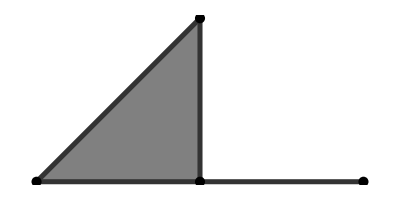

```mathematica
showCC2D[testCC]
```

Here is a 3D cell complex representing a cube:

```mathematica
testCC2={
(* 0-cells: point XYZ coordinates *)
{{0,0,0},{0,0,5},{0,5,0},{0,5,5},{5,0,0},{5,0,5},{5,5,0},{5,5,5}},
(* 1-cells: edges, each as a pair of indices of the end points of that edge *)
{{1,5},{2,6},{3,7},{4,8},{1,3},{2,4},{5,7},{6,8},{1,2},{3,4},{5,6},{7,8}},
(* 2-cells: faces, each as a list of indicies of the edges bounding that face *)
{{5,6,9,10},{7,8,11,12},{1,2,9,11},{3,4,10,12},{1,5,7,3},{2,6,8,4}},
(* 3-cells: cubes, each as a list of indicies of the faces bounding that cube *)
{{1,2,3,4,5,6}}};
```

Visualize this 3D cell complex with the showCC3D function in the Helper:

```mathematica
showCC3D[testCC2]
```

-Graphics3D-

### Conversion from binary pictures [12 pts]

Algorithm 1: [4 pts] Create a function that converts a 2D binary picture to a 2D cell complex. Your function should take in a single input (a 2-dimensional array with 0s and 1s), and output a cell complex in the above format. You may use either one of the two approaches introduced in the lecture (e.g., consistent with either 8-connectivity or 4-connectivity of the object in the binary picture).

Hint: You code should visit each pixel in the image and create new cells when appropriate. Make sure you do not re-create the same cell twice. To avoid duplication, you will need to store and retrieve the indices of 0-cells, 1-cells, 2-cells, etc as you move across the image. See lecture slides for an example of how to do so.

```mathematica
buildCC2D[array_]:=Module[
{nc,nr,cell,cell2,cell3,p,f,list,list1,list2,list3},
{nr,nc}=Dimensions[array];
list={};list1={};list2={};list3={};
p=Table[0,{4}];
f=Table[0,{4}];
Do[
Do[
cell={{j-1,i},{j-1,i-1},{j,i},{j,i-1}};
If[array[[i,j]]==1,
Do[
If[FreeQ[list1,cell[[k]]],
AppendTo[list1,cell[[k]]]];
{{p[[k]]}}=Position[list1,cell[[k]]],
{k,Length[cell]}];
cell2={{p[[1]],p[[2]]},{p[[3]],p[[4]]},{p[[1]],p[[3]]},{p[[2]],p[[4]]}};
Do[
If[FreeQ[list2,cell2[[k]]],
AppendTo[list2,cell2[[k]]]];
{{f[[k]]}}=Position[list2,cell2[[k]]],
{k,Length[cell2]}];
cell3={f[[1]],f[[2]],f[[3]],f[[4]]};
If[FreeQ[list3,cell3],
AppendTo[list3,cell3]]]
,{j,nc}]
,{i,nr}];
list=AppendTo[list,list1];
list=AppendTo[list,list2];
list=AppendTo[list,list3];
list]
```

Testing: [2pts] Test your functions with the following examples (and feel free to create your own), and check your results with the provided pictures (both 8- and 4- connectivity results are shown on the left and right)

Example 1:

```mathematica
arrC={{0,0,1,1,1},{1,1,0,1,1},{0,0,1,1,1}};
```

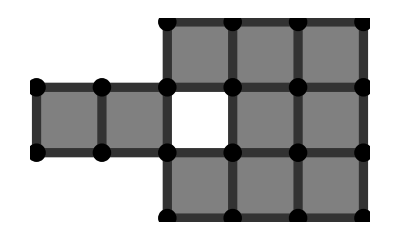

```mathematica
showCC2D[buildCC2D[arrC]]
```

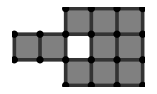
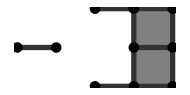

Example 2:

```mathematica
arrRing={{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,0,0,1,1},{1,1,0,0,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}};
```

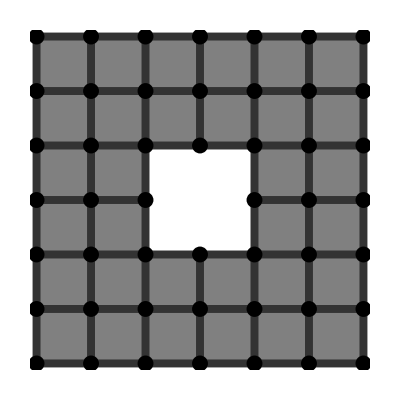

```mathematica
showCC2D[buildCC2D[arrRing]]
```

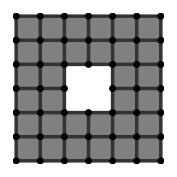
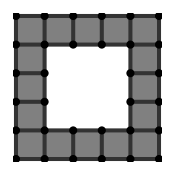

Example 3: load in the "horse_64.png", and use threshold 100 to create a binary picture.

```mathematica
threshold[img_,val_]:=Table[If[img[[i,j]]>val,1,0],{i,Dimensions[img][[1]]},{j,Dimensions[img][[2]]}]
```

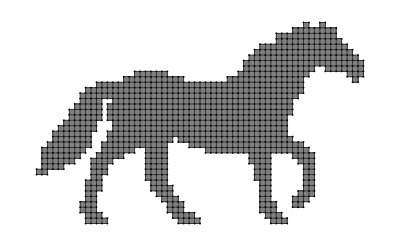

```mathematica
horse=PNGtoGray["horse_64.png"];
horse=threshold[horse,100];
showCC2D[buildCC2D[horse]]
```

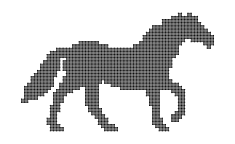
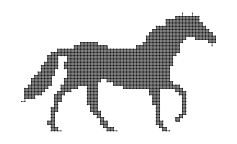

Algorithm 2: [4 pts] Create a function that converts a 3D binary picture to a 3D cell complex. Your function should take in a single input (a 3-dimensional array with 0s and 1s), and output a cell complex in the above format. You may use either one of the two approaches introduced in the lecture (e.g., consistent with either 26-connectivity or 6-connectivity of the object in the binary picture).

```mathematica
buildCC3D[array_]:=
```

Testing: [2pts] Test your functions with the following examples (and feel free to create your own), and check your results with the provided pictures (both 26- and 6- connectivity results are shown below on the left and right)

Example 1:

```mathematica
arrC3D={{{0,0},{0,0},{1,0},{1,0},{1,0}},{{1,0},{1,0},{0,0},{1,0},{1,0}},{{0,0},{0,0},{1,0},{1,0},{1,0}}};
```

```mathematica
buildCC3D[array_]:=Module[
{nx,ny,nz,cell,cell2,cell3,cell4,p,f,g,list,list1,list2,list3,list4},
{nx,ny,nz}=Dimensions[array];(*nx ny nz are x,y,z coordinates.*)
(*Initiate 5 lists of cellcomplex,0-cell,1-cell,2-cell,3-cell*)
list={};(*Cell complex*)
list1={};(*0-cell*)
list2={};(*1-cell*)
list3={};(*2-cell*)
list4={};(*3-cell*)
p=Table[0,{8}];
f=Table[0,{12}];
g=Table[0,{6}];
Do[
Do[
Do[
cell={{i-1,j-1,k-1},{i-1,j,k-1},{i,j-1,k-1},{i,j,k-1},{i-1,j-1,k},{i-1,j,k},{i,j-1,k},{i,j,k}};
If[array[[i,j,k]]==1,

Do[
If[FreeQ[list1,cell[[r]]],
AppendTo[list1,cell[[r]]]];
{{p[[r]]}}=Position[list1,cell[[r]]],
{r,8}];

cell2={
{p[[1]],p[[2]]},
{p[[2]],p[[4]]},
{p[[4]],p[[3]]},
{p[[1]],p[[3]]},
{p[[1]],p[[5]]},
{p[[2]],p[[6]]},
{p[[4]],p[[8]]},
{p[[3]],p[[7]]},
{p[[5]],p[[6]]},
{p[[6]],p[[8]]},
{p[[8]],p[[7]]},
{p[[5]],p[[7]]}
};

Do[
If[FreeQ[list2,cell2[[k]]],
AppendTo[list2,cell2[[k]]]];
{{f[[k]]}}=Position[list2,cell2[[k]]],
{k,12}];

cell3={
{f[[4]],f[[5]],f[[8]],f[[12]]},
{f[[3]],f[[7]],f[[8]],f[[11]]},
{f[[2]],f[[6]],f[[7]],f[[10]]},
{f[[1]],f[[5]],f[[6]],f[[9]]},
{f[[9]],f[[10]],f[[11]],f[[12]]},
{f[[1]],f[[2]],f[[3]],f[[4]]}
};

Do[
If[FreeQ[list3,cell3[[k]]],
AppendTo[list3,cell3[[k]]]];
{{g[[k]]}}=Position[list3,cell3[[k]]],
{k,6}];

cell4={g[[1]],g[[2]],g[[3]],g[[4]],g[[5]],g[[6]]};
list4=AppendTo[list4,cell4]]
,{k,nz}]
,{j,ny}]
,{i,nx}];
list=AppendTo[list,list1];
list=AppendTo[list,list2];
list=AppendTo[list,list3];
list =AppendTo[list,list4];
list]
```

```mathematica
showCC3D[buildCC3D[arrC3D]]
```

-Graphics3D-

```mathematica
{{1,2,3,4},{13,14,15,2},{21,22,23,14},{29,30,31,32},{41,42,43,30},{48,49,50,51},{58,59,60,49},{65,66,67,68},{75,76,77,66},{82,83,84,76}}
```

{{1,2,3,4},{13,14,15,2},{21,22,23,14},{29,30,31,32},{41,42,43,30},{48,49,50,51},{58,59,60,49},{65,66,67,68},{75,76,77,66},{82,83,84,76}}

```mathematica
-Graphics3D--Graphics3D-
```

Example 2:

```mathematica
arrRing3D={{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}},{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}},{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}},{{1,1},{1,1},{1,1},{0,0},{0,0},{1,1},{1,1},{1,1}},{{1,1},{1,1},{1,1},{0,0},{0,0},{1,1},{1,1},{1,1}},{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}},{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}},{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}}};
```

```mathematica
showCC3D[buildCC3D[arrRing3D]]
```

-Graphics3D-

```mathematica
-Graphics3D--Graphics3D-
```

Example 3: load the "tshape.dat" in the folder (using Get command, which will return a 3D binary picture).

```mathematica
tshape=Get["tshape.dat"];
```

```mathematica
r=buildCC3D[tshape];
```

$Aborted

```mathematica
showCC3D[r]
```

-Graphics3D-

```mathematica
-Graphics3D--Graphics3D-
```

### Thinning [10 pts]

Algorithm 3: [4 pts] Create a function that performs exhaustive, parallel thinning on a cell complex (all simple pairs are removed in each iteration, without preserving the medial cells). The function takes in a cell complex (which could be in 2D or 3D), and outputs another cell complex that is the resulting skeleton.

Hints:
1. To easily identify simple pairs, it is helpful to write a helper function that computes a table that stores, at each k-cell x, the number of (k+1)-cells (i.e., "parents") containing x on their boundary. Try to compute this parent table using a single pass over all the cells. With the table, you can identify a cell x as a simple cell if any of its children cells has exactly 1 parent. Again, you should be able to identify all simple pairs in a single pass over all the cells. Now, think about how to efficiently update the parent table after each iteration of thinning (without re-computing it by visiting all remaining cells).

2. Instead of explicitly removing the cells from the cell complex data structure at each iteration, a more efficient way is simply keeping a True/False tag at each cell indicating whether it is still in the complex. After thinning stops, you can then use these tags to remove all non-existent cells from the data structure in one pass. 

3. Be careful in updating the cell indices when removing the cells from the cell complex. For example, if the first cell in the list of k-cells is removed, any (k+1)-cell that uses the second cell in the original list of k-cells should now change the index of that k-cell from 2 to 1. Again, think about how to do so efficiently.

```mathematica
parentTable[imgCC_]:= Module[{t = List[],tt=List[],par,i,j},
For[ i =1,i≤ Length[imgCC],i++,tt = {};For[j = 1,j≤Length[imgCC⟦i⟧],j++,par = {};If[i == Length[imgCC],AppendTo[tt,0],AppendTo[par,Position[imgCC⟦i+1⟧,j]];AppendTo[tt,Length[par⟦1⟧]]]];AppendTo[t,tt]];t];
```

```mathematica
getTFtable[cc_]:= Module[{tab=List[],tabTemp},For[i = 1, i≤ Dimensions[cc]⟦1⟧,i++,tabTemp = {} ;For[j = 1,j≤ Length[cc⟦i⟧],j++,AppendTo[tabTemp,True]];AppendTo[tab,tabTemp]];tab];
```

```mathematica
remove[cc_,tab_]:= Module[{temp=List[],result=List[],rr=List[]},For[i=1,i≤ Length[tab],i++,temp={};For[j=1,j≤ Length[tab⟦i⟧],j++,If[tab⟦i⟧⟦j⟧,AppendTo[temp,cc⟦i⟧⟦j⟧]]];AppendTo[result,temp];];For[sup=1,sup≤Length[result],sup++,If[result⟦sup⟧!={},AppendTo[rr,result⟦sup⟧]]];rr];
```

```mathematica
thinExhaustive[cc_]:= Module[{k,c,d,h,tab=List[],s = List[],par = List[],rem=List[],result=List[]},tab=getTFtable[cc];par =parentTable[cc];result=cc;While[True,s = {};For[i =2, i≤ Dimensions[cc]⟦1⟧,i++,For[j = 1,j≤ Length[cc⟦i⟧],j++,If[tab⟦i⟧⟦j⟧,For[k =1,k≤ Length[cc⟦i⟧⟦j⟧],k++,If[par⟦i-1⟧⟦cc⟦i⟧⟦j⟧⟦k⟧⟧==1 && !MemberQ[rem,{i,j}]&& !MemberQ[rem,{i-1,cc⟦i⟧⟦j⟧⟦k⟧}], AppendTo[s,{{i,j},{i-1,cc⟦i⟧⟦j⟧⟦k⟧}}];AppendTo[rem,{i-1,cc⟦i⟧⟦j⟧⟦k⟧}];AppendTo[rem,{i,j}]];]]]];If[s=={},Break[],rem={};For[p=1,p≤ Length[s],p++,If[!MemberQ[rem,s⟦p⟧⟦1⟧]&&!MemberQ[rem,s⟦p⟧⟦2⟧], tab⟦s⟦p⟧⟦1⟧⟦1⟧⟧⟦s⟦p⟧⟦1⟧⟦2⟧⟧=False;If[s⟦p⟧⟦1⟧⟦1⟧+1≤ Dimensions[cc]⟦1⟧,For[a=1,a≤ Length[cc⟦s⟦p⟧⟦1⟧⟦1⟧+1⟧],a++,If[tab⟦s⟦p⟧⟦1⟧⟦1⟧+1⟧⟦a⟧,For[b=1,b≤ Length[cc⟦s⟦p⟧⟦1⟧⟦1⟧+1⟧⟦a⟧],b++,If[cc⟦s⟦p⟧⟦1⟧⟦1⟧+1⟧⟦a⟧⟦b⟧> s⟦p⟧⟦1⟧⟦2⟧,result⟦s⟦p⟧⟦1⟧⟦1⟧+1⟧⟦a⟧⟦b⟧=result⟦s⟦p⟧⟦1⟧⟦1⟧+1⟧⟦a⟧⟦b⟧-1;]]]]];tab⟦s⟦p⟧⟦2⟧⟦1⟧⟧⟦s⟦p⟧⟦2⟧⟦2⟧⟧=False;If[s⟦p⟧⟦2⟧⟦1⟧+1≤ Dimensions[cc]⟦1⟧,For[c=1,c≤ Length[cc⟦s⟦p⟧⟦2⟧⟦1⟧+1⟧],c++,If[tab⟦s⟦p⟧⟦2⟧⟦1⟧+1⟧⟦c⟧,For[d=1,d≤  Length[cc⟦s⟦p⟧⟦2⟧⟦1⟧+1⟧⟦c⟧],d++,If[cc⟦s⟦p⟧⟦2⟧⟦1⟧+1⟧⟦c⟧⟦d⟧> s⟦p⟧⟦2⟧⟦2⟧,result⟦s⟦p⟧⟦2⟧⟦1⟧+1⟧⟦c⟧⟦d⟧=result⟦s⟦p⟧⟦2⟧⟦1⟧+1⟧⟦c⟧⟦d⟧-1]]]]];For[h=1,h≤ Length[cc⟦s⟦p⟧⟦1⟧⟦1⟧⟧⟦s⟦p⟧⟦1⟧⟦2⟧⟧],h++,par⟦s⟦p⟧⟦1⟧⟦1⟧-1⟧⟦cc⟦s⟦p⟧⟦1⟧⟦1⟧⟧⟦s⟦p⟧⟦1⟧⟦2⟧⟧⟦h⟧⟧=par⟦s⟦p⟧⟦1⟧⟦1⟧-1⟧⟦cc⟦s⟦p⟧⟦1⟧⟦1⟧⟧⟦s⟦p⟧⟦1⟧⟦2⟧⟧⟦h⟧⟧-1];
If[s⟦p⟧⟦2⟧⟦1⟧-1>0,For[h=1,h≤ Length[result⟦s⟦p⟧⟦2⟧⟦1⟧⟧⟦s⟦p⟧⟦2⟧⟦2⟧⟧],h++,par⟦s⟦p⟧⟦2⟧⟦1⟧-1⟧⟦cc⟦s⟦p⟧⟦2⟧⟦1⟧⟧⟦s⟦p⟧⟦2⟧⟦2⟧⟧⟦h⟧⟧=par⟦s⟦p⟧⟦2⟧⟦1⟧-1⟧⟦cc⟦s⟦p⟧⟦2⟧⟦1⟧⟧⟦s⟦p⟧⟦2⟧⟦2⟧⟧⟦h⟧⟧-1];
];
]]];];remove[result,tab]];
```

Testing: [2pts] Test your function with 2D and 3D examples you have created above. Check your result (they should have the same topology as the original complexes while cannot be thinned further). Use the showCC2D, showCC3D functions to show the skeleton on top of the original complex.

```mathematica
ccccc =buildCC2D[arrC];
showCC2D[ccccc]
f = thinExhaustive[ccccc];
showCC2D[f,ccccc]
```

Algorithm 4: [2 pts] Modify your function above to perform thinning while protecting the medial cells. In addition to a cell complex, your function will take in an additional list containing the thresholds. The thresholds will be a list of pairs, so that the n-th pair are the thresholds for the absolute and relative differences between the isolation and removal iterations for the n-cells. For example, thinning a 2D complex would call thin[cc,{{5,0.5}}], and thinning a 3D complex may call thin[cc,{{5,0.5},{∞,1}}].

Hint: You can use the parent table you created for your exhaustive thinning function to quickly identify the isolated cells. Think about how to identify the isolated cells in an efficient way, without having to go through all the cells at each iteration (since you know exactly which cells are becoming "isolated" when you remove the simple pairs).

```mathematica
setIso[par_]:= Module[{I=List[],temp=List[]},For[i=1,i≤Length[par],i++,temp={};For[j=1,j≤Length[par⟦i⟧],j++,If[par⟦i⟧⟦j⟧==0,AppendTo[temp,0],AppendTo[temp,NULL]]];AppendTo[I,temp]];I];
```

```mathematica
absE[k_,i_,thr_]:=k-i>thr;
relE[k_,i_,thr_]:= ((k-i)/k)>thr;
```

```mathematica
thin[cc_,thresholds_]:=Module[{ss=List[],qqq=2,I=List[],tab=List[],s = List[],par = List[],rem=List[],result=List[]},tab=getTFtable[cc];par =parentTable[cc];I = setIso[par];result=cc;While[True,s = {};rem={};

For[i =2, i≤ Dimensions[cc]⟦1⟧,i++,For[j = 1,j≤ Length[cc⟦i⟧],j++,If[tab⟦i⟧⟦j⟧,For[k =1,k≤ Length[cc⟦i⟧⟦j⟧],k++,If[par⟦i-1⟧⟦cc⟦i⟧⟦j⟧⟦k⟧⟧==1 && !MemberQ[rem,{i,j}]&& !MemberQ[rem,{i-1,cc⟦i⟧⟦j⟧⟦k⟧}], AppendTo[s,{{i,j},{i-1,cc⟦i⟧⟦j⟧⟦k⟧}}];AppendTo[rem,{i-1,cc⟦i⟧⟦j⟧⟦k⟧}];AppendTo[rem,{i,j}]];]]]];ss = getTFtable[s];For[p=1,p≤Length[s],p++,If[s⟦p⟧⟦1⟧⟦1⟧==2 &&  par⟦s⟦p⟧⟦1⟧⟦1⟧⟧⟦s⟦p⟧⟦1⟧⟦2⟧⟧==0 &&absE[qqq,I⟦s⟦p⟧⟦1⟧⟦1⟧⟧⟦s⟦p⟧⟦1⟧⟦2⟧⟧,thresholds⟦1⟧⟦1⟧] && relE[qqq,I⟦s⟦p⟧⟦1⟧⟦1⟧⟧⟦s⟦p⟧⟦1⟧⟦2⟧⟧,thresholds⟦1⟧⟦2⟧],ss⟦p⟧=False];
If[Length[cc]==4&&par⟦s⟦p⟧⟦1⟧⟦1⟧⟧⟦s⟦p⟧⟦1⟧⟦2⟧⟧==0 &&s⟦p⟧⟦1⟧⟦1⟧==3 && absE[qqq,I⟦s⟦p⟧⟦1⟧⟦1⟧⟧⟦s⟦p⟧⟦1⟧⟦2⟧⟧,thresholds⟦2⟧⟦1⟧] && relE[qqq,I⟦s⟦p⟧⟦1⟧⟦1⟧⟧⟦s⟦p⟧⟦1⟧⟦2⟧⟧,thresholds⟦2⟧⟦2⟧],ss⟦p⟧=False]];s=remove[s,ss];If[s=={},Break[],For[p=1,p≤ Length[s],p++,tab⟦s⟦p⟧⟦1⟧⟦1⟧⟧⟦s⟦p⟧⟦1⟧⟦2⟧⟧=False;If[s⟦p⟧⟦1⟧⟦1⟧+1≤ Dimensions[cc]⟦1⟧,For[a=1,a≤ Length[cc⟦s⟦p⟧⟦1⟧⟦1⟧+1⟧],a++,If[tab⟦s⟦p⟧⟦1⟧⟦1⟧+1⟧⟦a⟧,For[b=1,b≤ Length[cc⟦s⟦p⟧⟦1⟧⟦1⟧+1⟧⟦a⟧],b++,If[cc⟦s⟦p⟧⟦1⟧⟦1⟧+1⟧⟦a⟧⟦b⟧> s⟦p⟧⟦1⟧⟦2⟧,result⟦s⟦p⟧⟦1⟧⟦1⟧+1⟧⟦a⟧⟦b⟧=result⟦s⟦p⟧⟦1⟧⟦1⟧+1⟧⟦a⟧⟦b⟧-1;]]]]];tab⟦s⟦p⟧⟦2⟧⟦1⟧⟧⟦s⟦p⟧⟦2⟧⟦2⟧⟧=False;If[s⟦p⟧⟦2⟧⟦1⟧+1≤ Dimensions[cc]⟦1⟧,For[c=1,c≤ Length[cc⟦s⟦p⟧⟦2⟧⟦1⟧+1⟧],c++,If[tab⟦s⟦p⟧⟦2⟧⟦1⟧+1⟧⟦c⟧,For[d=1,d≤  Length[cc⟦s⟦p⟧⟦2⟧⟦1⟧+1⟧⟦c⟧],d++,If[cc⟦s⟦p⟧⟦2⟧⟦1⟧+1⟧⟦c⟧⟦d⟧> s⟦p⟧⟦2⟧⟦2⟧,result⟦s⟦p⟧⟦2⟧⟦1⟧+1⟧⟦c⟧⟦d⟧=result⟦s⟦p⟧⟦2⟧⟦1⟧+1⟧⟦c⟧⟦d⟧-1]]]]];For[h=1,h≤ Length[cc⟦s⟦p⟧⟦1⟧⟦1⟧⟧⟦s⟦p⟧⟦1⟧⟦2⟧⟧],h++,par⟦s⟦p⟧⟦1⟧⟦1⟧-1⟧⟦cc⟦s⟦p⟧⟦1⟧⟦1⟧⟧⟦s⟦p⟧⟦1⟧⟦2⟧⟧⟦h⟧⟧=par⟦s⟦p⟧⟦1⟧⟦1⟧-1⟧⟦cc⟦s⟦p⟧⟦1⟧⟦1⟧⟧⟦s⟦p⟧⟦1⟧⟦2⟧⟧⟦h⟧⟧-1;If[par⟦s⟦p⟧⟦1⟧⟦1⟧-1⟧⟦cc⟦s⟦p⟧⟦1⟧⟦1⟧⟧⟦s⟦p⟧⟦1⟧⟦2⟧⟧⟦h⟧⟧==0,I⟦s⟦p⟧⟦1⟧⟦1⟧-1⟧⟦cc⟦s⟦p⟧⟦1⟧⟦1⟧⟧⟦s⟦p⟧⟦1⟧⟦2⟧⟧⟦h⟧⟧=qqq]];
If[s⟦p⟧⟦2⟧⟦1⟧-1>0,For[h=1,h≤ Length[result⟦s⟦p⟧⟦2⟧⟦1⟧⟧⟦s⟦p⟧⟦2⟧⟦2⟧⟧],h++,par⟦s⟦p⟧⟦2⟧⟦1⟧-1⟧⟦cc⟦s⟦p⟧⟦2⟧⟦1⟧⟧⟦s⟦p⟧⟦2⟧⟦2⟧⟧⟦h⟧⟧=par⟦s⟦p⟧⟦2⟧⟦1⟧-1⟧⟦cc⟦s⟦p⟧⟦2⟧⟦1⟧⟧⟦s⟦p⟧⟦2⟧⟦2⟧⟧⟦h⟧⟧-1;If[par⟦s⟦p⟧⟦2⟧⟦1⟧-1⟧⟦cc⟦s⟦p⟧⟦2⟧⟦1⟧⟧⟦s⟦p⟧⟦2⟧⟦2⟧⟧⟦h⟧⟧==0,I⟦s⟦p⟧⟦2⟧⟦1⟧-1⟧⟦cc⟦s⟦p⟧⟦2⟧⟦1⟧⟧⟦s⟦p⟧⟦2⟧⟦2⟧⟧⟦h⟧⟧=qqq]];
];
]];qqq=qqq+1;];remove[result,tab]];
```

```mathematica
A = buildCC2D[arrC];
showCC2D[thin[A,{{2,.4}}]]
showCC2D[thinExhaustive[A]]
```

Table::itform: Argument 2\ Dimensions[{{0, 0, 1, 1, 1}, {1, 1, 0, 1, 1}, {0, 0, 1, 1, 1}}] ⟦ 1 ⟧ + 1 at position 2 does not have the correct form for an iterator.

Table::itform: Argument 2\ Dimensions[{{0, 0, 1, 1, 1}, {1, 1, 0, 1, 1}, {0, 0, 1, 1, 1}}] ⟦ 2 ⟧ + 1 at position 2 does not have the correct form for an iterator.

Part::partw: Part 5 of Table[0, 2\ Dimensions[{{0, 0, 1, 1, 1}, {1, 1, 0, 1, 1}, {0, 0, 1, 1, 1}}] ⟦ 2 ⟧ + 1] does not exist.

Part::partw: Part 7 of Table[0, 2\ Dimensions[{{0, 0, 1, 1, 1}, {1, 1, 0, 1, 1}, {0, 0, 1, 1, 1}}] ⟦ 2 ⟧ + 1] does not exist.

Part::partw: Part 3 of Table[Table[0, 2\ Dimensions[{{« 5 »}, {« 5 »}, {« 5 »}}] ⟦ 2 ⟧ + 1], 2\ Dimensions[{{0, 0, 1, 1, 1}, {1, 1, 0, 1, 1}, {0, 0, 1, 1, 1}}] ⟦ 1 ⟧ + 1] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partd: Part specification 7 ⟦ 7 ⟧ is longer than depth of object.

Part::partd: Part specification 7 ⟦ 5 ⟧ is longer than depth of object.

Part::partd: Part specification 7 ⟦ 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression Point[1] cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression Point[1] cannot be used as a part specification.

```mathematica
thin[cc_,thresholds_]:=
```

Testing: [2pts] Test your function with the horse example in 2D and the tShape example in 3D (which you have converted from binary pictures). Check your result with the following pictures at these parameter settings:

2D horse example:

```mathematica
horse8=horse;
```

```mathematica
showCC2D[thin[horse8,{{∞,1}}],horse8]
```

Part::partw: Part 2 of getTFtable[{{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 14 »}, « 38 », {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 6 », 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 14 »}}] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

$Aborted

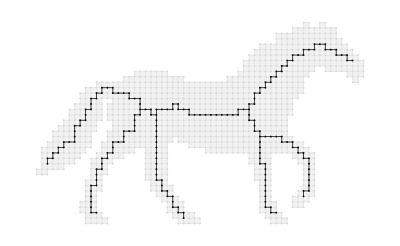

```mathematica
showCC2D[thin[horse8,{{4,.4}}],horse8]
```

3D Tshape example:

```mathematica
showCC3D[thin[tShape26,{{∞,1},{∞,1}}],tShape26]
```

-Graphics3D-

```mathematica
showCC3D[thin[tShape26,{{∞,1},{5,.5}}],tShape26]
```

-Graphics3D-

```mathematica
showCC3D[thin[tShape26,{{4,.4},{∞,1}}],tShape26]
```

-Graphics3D-

```mathematica
showCC3D[thin[tShape26,{{4,.4},{5,.5}}],tShape26]
```

-Graphics3D-

## Problems

Use your thinning code to compute skeletons of these 2D and 3D shapes.

### Leaf epidermis [2 pts]

Problem 1: [1 pts] See image in "epidermis.png" shown on the left. Compute a curve skeleton that best represents the curved features in the image (an example is on the right). Use the showCC2DImg function to view skeletons overlayed on the image.

```mathematica
-Graphics--Graphics-
```

### Micro filaments [2 pts]

Problem 2: [1 pts] See image in "filament_part.png" shown on the left. Compute a curve skeleton that best represents the line features in the image (an example is on the right).

```mathematica
-Graphics--Graphics-
```

### Human hand [2 pts]

Problem 3: [2 pts] Load the 3D binary picture in "hand.dat", and compute the three types of skeletons as shown below.

```mathematica
-Graphics3D--Graphics3D-
```

```mathematica
-Graphics3D--Graphics3D-
```